## The code for Example 4.7.

```mathematica
A = {{0,1,2},{1,0,2},{4,1,0},{1,3,0}};
B = {{0,4,3,2},{4,0,1,1},{4,1,0,4}};

A.B//MatrixForm
```

(12 | 2 | 1 | 9
8 | 6 | 3 | 10
4 | 16 | 13 | 9
12 | 4 | 6 | 5)

```mathematica
M1 = A.B
```

{{12,2,1,9},{8,6,3,10},{4,16,13,9},{12,4,6,5}}

#### (1,1) entry missing

```mathematica
A2 = A;
A2[[4,3]]=-1;
```

```mathematica
M2 = A2.B;
M2[[1,1]]=x;
M2//MatrixForm
```

(x | 2 | 1 | 9
8 | 6 | 3 | 10
4 | 16 | 13 | 9
8 | 3 | 6 | 1)

```mathematica
xsol = Solve[Det[M2]==0,x]
M2 = M2/.xsol[[1]]
```

{{x→12}}

{{12,2,1,9},{8,6,3,10},{4,16,13,9},{8,3,6,1}}

```mathematica
(* Compute line between the points {x1,y1} and {x2,y2} *)
line[{x1_,y1_},{x2_,y2_}]:=If[x1 -x2!=0, (y2-y1)/(x2-x1)*x-y+(y2- (y2-y1)/(x2-x1)*x2),x-x1];

(* See if line l supports the polygon with vertices a1,a2,a3,a4 returns True or False *)
supp[l_, a1_,a2_,a3_,a4_]:=
Module[{vals},vals=Block[{x,y},
{l/. {x->a1[[1]],y->a1[[2]]},
l/. {x->a2[[1]],y->a2[[2]]},
l/. {x->a3[[1]],y->a3[[2]]},
l/. {x->a4[[1]],y->a4[[2]]}}];
Simplify[(And@@Thread[vals>=0])||(And@@Thread[vals<=0])]
]

(* Given outer vertex q and inner vertices a1,a2,a3,a4, find the two lines q-ai and q-aj such that the lines q-ai and q-aj support the polygon with the inner vertices, returns list with the lines that are supporting the inner polygon *)
findSupportingLines[q_,a1_,a2_,a3_,a4_]:=Module[{l1,l2,l3,l4,supportingLines},
l1=line[q,a1];
l2=line[q,a2];
l3=line[q,a3];
l4=line[q,a4];
supportingLines={};
If[l1 =!= Nothing &&supp[l1,a1,a2,a3,a4],AppendTo[supportingLines,l1]];
If[l2 =!= Nothing &&supp[l2,a1,a2,a3,a4],AppendTo[supportingLines,l2]];
If[l3 =!= Nothing &&supp[l3,a1,a2,a3,a4],AppendTo[supportingLines,l3]];
If[l4 =!= Nothing &&supp[l4,a1,a2,a3,a4],AppendTo[supportingLines,l4]];
Return[supportingLines];
];

(* Find the intersection of line l with boundary defined by s1,s2,s3,s4. Returns the intersection point v={x,y} that is not the point q *)
findIntersectionWithBoundary[l_,s1_,s2_,s3_,s4_,ineqsQ_,q_]:=Module[{linesToCheck,solsubs,v}, 
linesToCheck={s1,s2,s3,s4};
For[i=1,i<=Length[linesToCheck],i++, solsubs= Solve[l==0 && linesToCheck[[i]]==0 &&ineqsQ, {x,y},Reals]; If[solsubs =!= {}, 
v = {x,y}/.solsubs[[1]]; 
If[v[[1]]!= q[[1]] ||v[[2]]!=q[[2]], Return[v]]
];
];
Nothing
];

(* Check if inner polygon is contained in triangle. INPUT: the edges of triangle and inner vertices. Checks if edges of triangle support inner polygon. Returns True or False *)
isContained[l1v1_,l1v2_ ,lv1v2_,a1_,a2_,a3_,a4_]:=
Module[{res},res=supp[l1v1,a1,a2,a3,a4]&&supp[l1v2,a1,a2,a3,a4]&&supp[lv1v2,a1,a2,a3,a4];
If[res == True,Print["True: This is a triangle nested in between P and Q."],Print["False: This triangle is not nested between P and Q"]];
Return[res] 
]
```

```mathematica
rowsums = Total/@M2;
Sm = DiagonalMatrix[rowsums];

Browsums = Total/@B;
Om = {{Browsums[[1]],0,0},{Browsums[[2]],1,0},{Browsums[[3]],0,1}};
Atildepol = Inverse[Sm].A2. Om;
Atildepol//FullSimplify//MatrixForm
Btildepol = Inverse[Om].B;
Btildepol//Simplify//MatrixForm

(* Check that factorization was defined correctly *)
Inverse[Sm].M2 == Atildepol.Btildepol//FullSimplify
```

(1 | 1/24 | 1/12
1 | 0 | 2/27
1 | 1/42 | 0
1 | 1/6 | -1/18)

(0 | 4/9 | 1/3 | 2/9
4 | -8/3 | -1 | -1/3
4 | -3 | -3 | 2)

True

```mathematica
(* Outer polytope *)
ineqsQ=And@@Thread[(({1,x,y}).#>=0)&/@Transpose[Btildepol]]//Simplify
q1 = {x,y}/.Solve[x+y==0&&3 x+9 y==1, {x,y}][[1]];
q2 = {x,y}/.Solve[x+y==0&&x==2/3+6 y, {x,y}][[1]];
q3 = {x,y}/.Solve[24 x+27 y==4&&x==2/3+6 y, {x,y}][[1]];
q4 = {x,y}/.Solve[24 x+27 y==4&&3 x+9 y==1, {x,y}][[1]];
s1 = x+y;
s2 =24 x+27 y-4;
s3 =3 x+9 y-1;
s4 = -x+2/3+6 y;


(* Inner polytope *)
verticesP = Atildepol[[1;;,2;;]]//Simplify;
p1 = verticesP[[1,All]];
p2 = verticesP[[2,All]];
p3 = verticesP[[3,All]];
p4 = verticesP[[4,All]];
```

x+y≥0&&24 x+27 y≤4&&3 x+9 y≤1&&x≤2/3+6 y

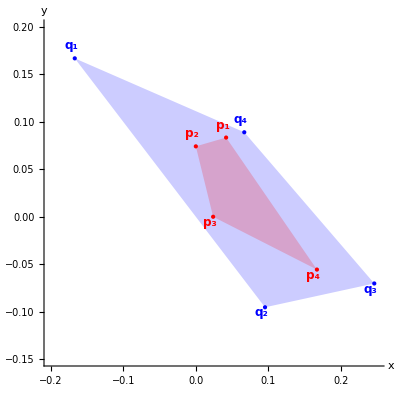

```mathematica
(*Vertices of outer polygon Q*)
qVertices={q1,q2,q3,q4};
qLabels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p2,p3,p4};
pLabels={Subscript["p",1],Subscript["p",2],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q*)
Style[Polygon[qVertices],Opacity[0.2],Blue],
(*Mark the vertices of inner polygon P*)
Blue,PointSize[Large],Point[qVertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Large],Point[pVertices],

(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[qLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
qVertices[[i]]+If[i==2 ||i==3,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[qVertices]}],
(*Add labels to inner polygon P vertices*)
Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==3 ||i==4,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[pVertices]}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.2,0.25},{-0.15,0.2}},AspectRatio->1
]
```

```mathematica
(* Vertex q1 *)
q1supportingLines =  findSupportingLines[q1,p1,p2,p3,p4];

v1 = findIntersectionWithBoundary[q1supportingLines[[1]],s1,s2,s3,s4,ineqsQ,q1];

v2 = findIntersectionWithBoundary[q1supportingLines[[2]],s1,s2,s3,s4,ineqsQ,q1];

(* Convex hull of q1,v1,v2*)

l1v1= line[q1,v1];
l1v2=line[q1,v2];
lv1v2 = line[v1,v2];

isContained[l1v1,l1v2,lv1v2, p1,p2,p3,p4]
```

False: This triangle is not nested between P and Q

False

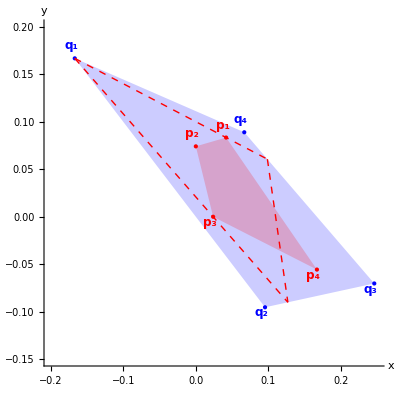

```mathematica
(*Vertices of outer polygon Q*)
qVertices={q1,q2,q3,q4};
qLabels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p2,p3,p4};
pLabels={Subscript["p",1],Subscript["p",2],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q*)
Style[Polygon[qVertices],Opacity[0.2],Blue],
(*Mark the vertices of inner polygon P*)
Blue,PointSize[Large],Point[qVertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Large],Point[pVertices],

(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[qLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
qVertices[[i]]+If[i==2 ||i==3,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[qVertices]}],
(*Add labels to inner polygon P vertices*)
Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==3 ||i==4,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[pVertices]}],
Dashed,Line[{q1,v1}],Line[{q1,v2}], Line[{v1,v2}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.2,0.25},{-0.15,0.2}},AspectRatio->1
]
```

```mathematica
(* Vertex q2 *)
outervertex = q2;
supportingLines =  findSupportingLines[outervertex,p1,p2,p3,p4];

v1 = findIntersectionWithBoundary[supportingLines[[1]],s1,s2,s3,s4,ineqsQ,outervertex];

v2 = findIntersectionWithBoundary[supportingLines[[2]],s1,s2,s3,s4,ineqsQ,outervertex];

(* Convex hull of q1,v1,v2*)

l1v1= line[outervertex,v1];
l1v2=line[outervertex,v2];
lv1v2 = line[v1,v2];

isContained[l1v1,l1v2,lv1v2, p1,p2,p3,p4]
```

False: This triangle is not nested between P and Q

False

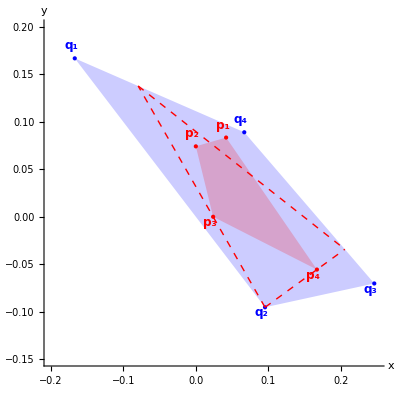

```mathematica
(*Vertices of outer polygon Q*)
qVertices={q1,q2,q3,q4};
qLabels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p2,p3,p4};
pLabels={Subscript["p",1],Subscript["p",2],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q*)
Style[Polygon[qVertices],Opacity[0.2],Blue],
(*Mark the vertices of inner polygon P*)
Blue,PointSize[Large],Point[qVertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Large],Point[pVertices],

(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[qLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
qVertices[[i]]+If[i==2 ||i==3,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[qVertices]}],
(*Add labels to inner polygon P vertices*)
Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==3 ||i==4,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[pVertices]}],
Dashed,Line[{outervertex,v1}],Line[{outervertex,v2}], Line[{v1,v2}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.2,0.25},{-0.15,0.2}},AspectRatio->1
]
```

```mathematica
(* Vertex q3 *)
outervertex = q3;
supportingLines =  findSupportingLines[outervertex,p1,p2,p3,p4];

v1 = findIntersectionWithBoundary[supportingLines[[1]],s1,s2,s3,s4,ineqsQ,outervertex];

v2 = findIntersectionWithBoundary[supportingLines[[2]],s1,s2,s3,s4,ineqsQ,outervertex];

(* Convex hull of q1,v1,v2*)

l1v1= line[outervertex,v1];
l1v2=line[outervertex,v2];
lv1v2 = line[v1,v2];

isContained[l1v1,l1v2,lv1v2, p1,p2,p3,p4]
```

False: This triangle is not nested between P and Q

False

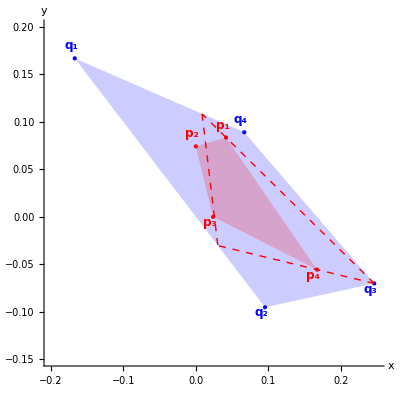

```mathematica
(*Vertices of outer polygon Q*)
qVertices={q1,q2,q3,q4};
qLabels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p2,p3,p4};
pLabels={Subscript["p",1],Subscript["p",2],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q*)
Style[Polygon[qVertices],Opacity[0.2],Blue],
(*Mark the vertices of inner polygon P*)
Blue,PointSize[Large],Point[qVertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Large],Point[pVertices],

(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[qLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
qVertices[[i]]+If[i==2 ||i==3,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[qVertices]}],
(*Add labels to inner polygon P vertices*)
Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==3 ||i==4,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[pVertices]}],
Dashed,Line[{outervertex,v1}],Line[{outervertex,v2}], Line[{v1,v2}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.2,0.25},{-0.15,0.2}},AspectRatio->1
]
```

```mathematica
(* Vertex q4 *)
outervertex = q4;
supportingLines =  findSupportingLines[outervertex,p1,p2,p3,p4];

v1 = findIntersectionWithBoundary[supportingLines[[3]],s1,s2,s3,s4,ineqsQ,outervertex];

v2 = findIntersectionWithBoundary[supportingLines[[2]],s1,s2,s3,s4,ineqsQ,outervertex];

(* Convex hull of q1,v1,v2*)

l1v1= line[outervertex,v1];
l1v2=line[outervertex,v2];
lv1v2 = line[v1,v2];

isContained[l1v1,l1v2,lv1v2, p1,p2,p3,p4]
```

False: This triangle is not nested between P and Q

False

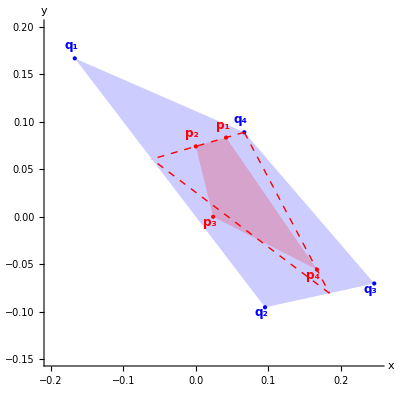

```mathematica
(*Vertices of outer polygon Q*)
qVertices={q1,q2,q3,q4};
qLabels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p2,p3,p4};
pLabels={Subscript["p",1],Subscript["p",2],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q*)
Style[Polygon[qVertices],Opacity[0.2],Blue],
(*Mark the vertices of inner polygon P*)
Blue,PointSize[Large],Point[qVertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Large],Point[pVertices],

(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[qLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
qVertices[[i]]+If[i==2 ||i==3,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[qVertices]}],
(*Add labels to inner polygon P vertices*)
Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==3 ||i==4,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[pVertices]}],
Dashed,Line[{outervertex,v1}],Line[{outervertex,v2}], Line[{v1,v2}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.2,0.25},{-0.15,0.2}},AspectRatio->1
]
```

### Algorithm for inner edges of P.

```mathematica
(*Intersection point of the lines l1 and l2*)
point[l1_,l2_]:=Module[{sol},
sol = Solve[l1==0&&l2==0,{x,y}, Reals];
If[sol=!= {},{x,y}/.sol[[1]], Nothing]
]

(*Function to safely extract a point from Solve results, with check that solution is not empty *)
getPointFromSolve[eqs_,vars_]:=Module[{sol},
sol=Solve[eqs,vars,Reals];
If[sol=!={},vars/. First[sol],Nothing ]
];

(* Find the two intersection points of the line l with the boundaries s1,s2,s3,s4, satisfying the inequalities defined by ineqsQ. Returns list of intersection points vi = {xi,yi} *)
findIntersectionWithBoundaryTwoPoints[l_,s1,s2,s3,s4,ineqsQ]:= Module[{linesToCheck,intersections, v,vsubs,res},
linesToCheck={s1,s2,s3,s4};
intersections={};
For[i=1,i<=Length[linesToCheck],i++,
v=point[l,linesToCheck[[i]]];
vsubs= {x->v[[1]],y->v[[2]]};
res = Reduce[ineqsQ/.vsubs];
If[res==True, AppendTo[intersections, v]]
];
Return[intersections]
];

(* Given vertex v, find out whether the line v--innerv1 or v--innerv2 supports the polygon with vertices a1,a2,a3,a4. Returns the line l that supports the polygon. *)
findSupportingVertex[v_,innerv1_,innerv2_ ,a1_,a2_,a3_,a4_]:=Module[{innervertices,l},
innervertices = {innerv1,innerv2};
For[i=1,i<=Length[innervertices],i++,
l = line[v,innervertices[[i]]];
If [supp[l,a1,a2,a3,a4] == True, Return[l]]
]
];
```

```mathematica
(* inner edge l12 *)
l = line[p1,p2];
ClearAll[linesToCheck,intersections];
intersections= findIntersectionWithBoundaryTwoPoints[l,s1,s2,s3,s4,ineqsQ];
v1 = intersections[[1]];
v2=intersections[[2]];

l1 = findSupportingVertex[v1,p3,p4, p1,p2,p3,p4];
l2 =  findSupportingVertex[v2,p3,p4, p1,p2,p3,p4];

v3 = point[l1,l2];

v3subs= {x->v3[[1]],y->v3[[2]]};
Print["The triangle is nested between P and Q:",Reduce[ineqsQ/.v3subs]]
```

The triangle is nested between P and Q:False

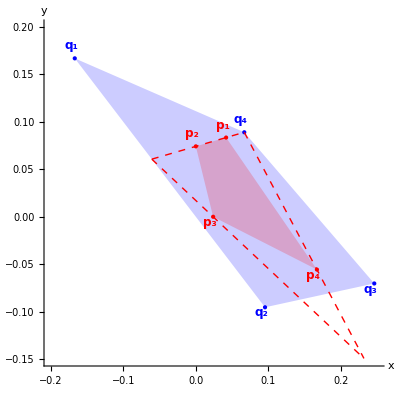

```mathematica
(*Vertices of outer polygon Q*)
qVertices={q1,q2,q3,q4};
qLabels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p2,p3,p4};
pLabels={Subscript["p",1],Subscript["p",2],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q*)
Style[Polygon[qVertices],Opacity[0.2],Blue],
(*Mark the vertices of inner polygon P*)
Blue,PointSize[Large],Point[qVertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Large],Point[pVertices],

(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[qLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
qVertices[[i]]+If[i==2 ||i==3,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[qVertices]}],
(*Add labels to inner polygon P vertices*)
Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==3 ||i==4,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[pVertices]}],
Dashed,Line[{v1,v2}],Line[{v1,v3}], Line[{v2,v3}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.2,0.25},{-0.15,0.2}},AspectRatio->1
]
```

```mathematica
(* inner edge l14 *)
l = line[p1,p4];
ClearAll[linesToCheck,intersections];
intersections= findIntersectionWithBoundaryTwoPoints[l,s1,s2,s3,s4,ineqsQ];
v1 = intersections[[1]];
v2=intersections[[2]];

l1 = findSupportingVertex[v1,p3,p2, p1,p2,p3,p4];
l2 =  findSupportingVertex[v2,p3,p2, p1,p2,p3,p4];

v3 = point[l1,l2];

v3subs= {x->v3[[1]],y->v3[[2]]};
Print["The triangle is nested between P and Q:",Reduce[ineqsQ/.v3subs]]
```

The triangle is nested between P and Q:False

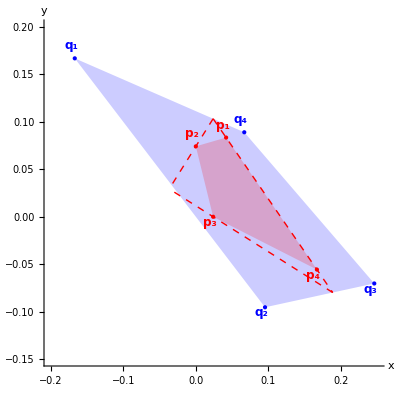

```mathematica
(*Vertices of outer polygon Q*)
qVertices={q1,q2,q3,q4};
qLabels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p2,p3,p4};
pLabels={Subscript["p",1],Subscript["p",2],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q*)
Style[Polygon[qVertices],Opacity[0.2],Blue],
(*Mark the vertices of inner polygon P*)
Blue,PointSize[Large],Point[qVertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Large],Point[pVertices],

(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[qLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
qVertices[[i]]+If[i==2 ||i==3,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[qVertices]}],
(*Add labels to inner polygon P vertices*)
Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==3 ||i==4,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[pVertices]}],
Dashed,Line[{v1,v2}],Line[{v1,v3}], Line[{v2,v3}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.2,0.25},{-0.15,0.2}},AspectRatio->1
]
```

```mathematica
(* inner edge l23 *)
l = line[p2,p3];
ClearAll[linesToCheck,intersections];
intersections= findIntersectionWithBoundaryTwoPoints[l,s1,s2,s3,s4,ineqsQ];
v1 = intersections[[1]];
v2=intersections[[2]];

l1 = findSupportingVertex[v1,p1,p4, p1,p2,p3,p4];
l2 =  findSupportingVertex[v2,p1,p4, p1,p2,p3,p4];

v3 = point[l1,l2];

v3subs= {x->v3[[1]],y->v3[[2]]};
Print["The triangle is nested between P and Q:",Reduce[ineqsQ/.v3subs]]
```

The triangle is nested between P and Q:False

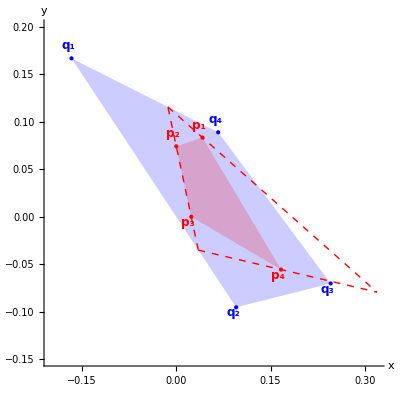

```mathematica
(*Vertices of outer polygon Q*)
qVertices={q1,q2,q3,q4};
qLabels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p2,p3,p4};
pLabels={Subscript["p",1],Subscript["p",2],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q*)
Style[Polygon[qVertices],Opacity[0.2],Blue],
(*Mark the vertices of inner polygon P*)
Blue,PointSize[Large],Point[qVertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Large],Point[pVertices],

(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[qLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
qVertices[[i]]+If[i==2 ||i==3,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[qVertices]}],
(*Add labels to inner polygon P vertices*)
Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==3 ||i==4,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[pVertices]}],
Dashed,Line[{v1,v2}],Line[{v1,v3}], Line[{v2,v3}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.2,0.32},{-0.15,0.2}},AspectRatio->1
]
```

```mathematica
(* inner edge l34 *)
l = line[p4,p3];
ClearAll[linesToCheck,intersections];
intersections= findIntersectionWithBoundaryTwoPoints[l,s1,s2,s3,s4,ineqsQ];
v1 = intersections[[1]];
v2=intersections[[2]];

l1 = findSupportingVertex[v1,p1,p2, p1,p2,p3,p4];
l2 =  findSupportingVertex[v2,p1,p2, p1,p2,p3,p4];

v3 = point[l1,l2];

v3subs= {x->v3[[1]],y->v3[[2]]};
Print["The triangle is nested between P and Q: ",Reduce[ineqsQ/.v3subs]]
```

The triangle is nested between P and Q: False

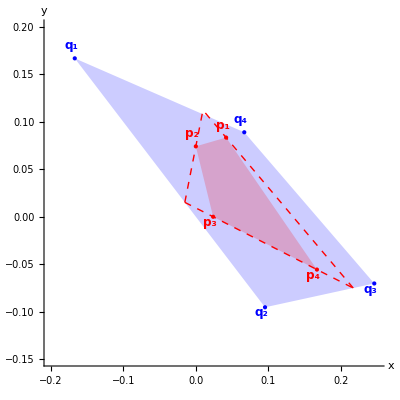

```mathematica
(*Vertices of outer polygon Q*)
qVertices={q1,q2,q3,q4};
qLabels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p2,p3,p4};
pLabels={Subscript["p",1],Subscript["p",2],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q*)
Style[Polygon[qVertices],Opacity[0.2],Blue],
(*Mark the vertices of inner polygon P*)
Blue,PointSize[Large],Point[qVertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Large],Point[pVertices],

(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[qLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
qVertices[[i]]+If[i==2 ||i==3,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[qVertices]}],
(*Add labels to inner polygon P vertices*)
Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==3 ||i==4,{-0.005,-0.006},{-0.005,0.013}]],{i,Length[pVertices]}],
Dashed,Line[{v1,v2}],Line[{v1,v3}], Line[{v2,v3}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.2,0.25},{-0.15,0.2}},AspectRatio->1
]
```